```mathematica
x=Cos[s*2π]
```

Cos[2 π s]

```mathematica
y=Sin[2*π*s]
```

Sin[2 π s]

```mathematica
z=Sin[2*π*2s]
```

Sin[4 π s]

```mathematica
p={x,y,z}
```

{Cos[2 π s],Sin[2 π s],Sin[4 π s]}

```mathematica
pathplot=ParametricPlot3D[{x,y,z},{s,0,1}]
```

-Graphics3D-

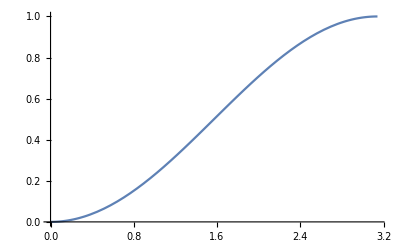

```mathematica
Plot[(1-Cos[α])/2,{α,0,π}]
```

```mathematica
Tvec=D[{x,y,z},{s}]
```

{-2 π Sin[2 π s],2 π Cos[2 π s],4 π Cos[4 π s]}

```mathematica
norm[v_]:=Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2];
```

```mathematica
Tunit=Simplify[Tvec/norm[Tvec]]
```

{-Sin[2 π s]/(√(3+2 Cos[8 π s])),Cos[2 π s]/(√(3+2 Cos[8 π s])),(2 Cos[4 π s])/(√(3+2 Cos[8 π s]))}

```mathematica
cyl1=Graphics3D[Cylinder[{p,p+Tunit*.1},0.05]]/.s-> 0
```

-Graphics3D-

```mathematica
cyl2=Graphics3D[Cylinder[{p,p+Tunit*.1},0.05]]/.s-> .1
```

-Graphics3D-

```mathematica
cyl={cyl1,cyl2}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
cyl=Table[Graphics3D[Cylinder[{p,p+Tunit*.1},0.05]]/.s-> i,{i,0,1,.01}];
```

```mathematica
Show[pathplot,cyl]
```

-Graphics3D-

```mathematica
R={{q0^2+q1^2-q2^2-q3^2,2 q1 q2-2 q0 q3,2 q1 q3+2 q0 q2},{2 q1 q2+2 q0 q3,q0^2-q1^2+q2^2-q3^2,2 q2 q3-2 q0 q1},{2 q1 q3-2 q0 q2,2 q2 q3+2 q0 q1,q0^2-q1^2-q2^2+q3^2}};
```

```mathematica
Det[{{q0^2+q1^2-q2^2-q3^2,2 q1 q2-2 q0 q3,2 q0 q2+2 q1 q3},{2 q1 q2+2 q0 q3,q0^2-q1^2+q2^2-q3^2,-2 q0 q1+2 q2 q3},{-2 q0 q2+2 q1 q3,2 q0 q1+2 q2 q3,q0^2-q1^2-q2^2+q3^2}}]
```

q0^6+3 q0^4 q1^2+3 q0^2 q1^4+q1^6+3 q0^4 q2^2+6 q0^2 q1^2 q2^2+3 q1^4 q2^2+3 q0^2 q2^4+3 q1^2 q2^4+q2^6+3 q0^4 q3^2+6 q0^2 q1^2 q3^2+3 q1^4 q3^2+6 q0^2 q2^2 q3^2+6 q1^2 q2^2 q3^2+3 q2^4 q3^2+3 q0^2 q3^4+3 q1^2 q3^4+3 q2^2 q3^4+q3^6

```mathematica
input={q0->-0.2,q1->0.3,q2->1/Sqrt[2],q3->Sqrt[1-1/2-0.3^2-.2^2],r1->2,r2->2.5,l1->12,l2->18,tx->8,ty->-8,tz->8};
Show[Graphics3D[{Opacity[0.5],Cylinder[{{0,0,0},{0,0,l1/.input}},r1/.input]}],Graphics3D[Cylinder[{({tx,ty,tz})/.input,({tx,ty,tz}+R.{0,0,l2/.input})/.input},r2/.input]],Boxed->False]
```

-Graphics3D-

```mathematica
input1={q0->-0.2,q1->0.3,q2->1/Sqrt[3],q3->Sqrt[1-1/3-0.3^2-.2^2],r1->2,r2->2.5,l1->12,l2->18,tx->6,ty->-6,tz->6};
Show[Graphics3D[{Opacity[0.5],Cylinder[{{0,0,0},{0,0,l1/.input1}},r1/.input1]}],Graphics3D[Cylinder[{({tx,ty,tz})/.input1,({tx,ty,tz}+R.{0,0,l2/.input1})/.input1},r2/.input1]],Boxed->False]
```

-Graphics3D-

```mathematica
input1={q0->1/Sqrt[2],q1->1/Sqrt[3],q2->0,q3->1-1/2-1/3,r1->2,r2->2.5,l1->12,l2->18,tx->6,ty->15,tz->6};
Show[Graphics3D[{Opacity[0.5],Cylinder[{{0,0,0},{0,0,l1/.input1}},r1/.input1]}],Graphics3D[Cylinder[{({tx,ty,tz})/.input1,({tx,ty,tz}+R.{0,0,l2/.input1})/.input1},r2/.input1]],Boxed->False]
```

-Graphics3D-

```mathematica
input1={q0->0,q1->-1/Sqrt[2],q2->0,q3->1-1/2,r1->2,r2->2.5,l1->12,l2->18,tx->6,ty->15,tz->6};
Show[Graphics3D[{Opacity[0.5],Cylinder[{{0,0,0},{0,0,l1/.input1}},r1/.input1]}],Graphics3D[Cylinder[{({tx,ty,tz})/.input1,({tx,ty,tz}+R.{0,0,l2/.input1})/.input1},r2/.input1]],Boxed->False]
```

-Graphics3D-

```mathematica
zeroQ[a_,eps_: 10^(-10)]:=Module[{},If[NumericQ[a]&&Abs[a]<eps,Return[True];,Return[False];];];

rottoAxisAngle[R_,k_,ϕ_]:=Module[{solϕ,sϕ,solk,sol},(*Check to make sure the dimensions of the rotation matrix are correct*)If[!MatrixQ[R]||Dimensions[R]≠{3,3},Print["rottoAxisAngle::error: ",R," is not a 3x3 matrix!"];
Return[{}];];
solϕ={ϕ->ArcCos[(Tr[R]-1)/2]};
sϕ=Sin[ϕ]/.solϕ;
If[zeroQ[solϕ],Print["rottoAxisAngle::error: angle is calculated as 0,π or -π. Hence, the axis cannot be found."];
Return[{}];];
solk={k->(1/(2*sϕ))*{R[[3,2]]-R[[2,3]],R[[1,3]]-R[[3,1]],R[[2,1]]-R[[1,2]]}};
sol=Union[solk,solϕ];
Return[sol];];

axisAngletoRot[{kx_,ky_,kz_},ϕ_]:=Module[{cϕ,sϕ,omincϕ,kxsϕ,kysϕ,kzsϕ,kxy,kyz,kzx,sol},cϕ=Cos[ϕ];
sϕ=Sin[ϕ];
omincϕ=1-cϕ;
kxsϕ=kx*sϕ;
kysϕ=ky*sϕ;
kzsϕ=kz*sϕ;
kxy=kx*ky*omincϕ;
kyz=ky*kz*omincϕ;
kzx=kz*kx*omincϕ;
sol={{kx*kx*omincϕ+cϕ,kxy-kzsϕ,kzx+kysϕ},{kxy+kzsϕ,ky*ky*omincϕ+cϕ,kyz-kxsϕ},{kzx-kysϕ,kyz+kxsϕ,kz*kz*omincϕ+cϕ}};
Return[sol];];
```

```mathematica
o2i={-3,6,6}
o2f={6,8,6}
subsall={r1->2,r2->2.5,l1->12,l2->18};
inputi={q0->0,q1->-1/Sqrt[2],q2->0,q3->Sqrt[1-1/2]};inputf={q0->0,q1->1/Sqrt[2],q2->0,q3->Sqrt[1-1/2]};
```

{-3,6,6}

{6,8,6}

```mathematica
Rnet=Transpose[R/.inputi].(R/.inputf)//Simplify
```

{{-1,0,0},{0,1,0},{0,0,-1}}

```mathematica
Det[Rnet]
```

1

```mathematica
o2=o2i+(o2f-o2i)*s
```

{-3+9 s,6+2 s,6}

```mathematica
kphi=rottoAxisAngle[Rnet,k,ϕ]//Simplify
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{k→{Indeterminate,Indeterminate,Indeterminate},ϕ→π}

```mathematica
rots=axisAngletoRot[k/.kphi,ϕ*s/.kphi]/.subsall//Simplify
```

{{Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate}}

```mathematica
Rs=(R/.inputi).rots/.subsall//Simplify
```

{{Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate}}

```mathematica
cylpath=Table[Graphics3D[{Opacity[0.3],Cylinder[{o2/.s-> i,(o2+Rs.{0,0,l2/.subsall})/.s-> i},r2/.subsall]}],{i,0,1,.05}];
```

```mathematica
Clear[s]
```

```mathematica
cyl1=Graphics3D[{Opacity[0.5],Cylinder[{{0,0,0},{0,0,l1/.subsall}},r1/.subsall]}];
```

```mathematica
Show[cylpath,cyl1,Axes-> True]
```

-Graphics3D-